## Splines paramétricos

```mathematica
cubic[data_]:=Module[{l=Length[data]},
s=Table[{Subscript[ax, i]+Subscript[bx, i] t+Subscript[cx, i] t^2+Subscript[dx, i] t^3,Subscript[ay, i]+Subscript[by, i] t+Subscript[cy, i] t^2+Subscript[dy, i] t^3},{i,l-1}];
c1=Flatten[Table[{(s[[i,1]]/.t->0)==data[[i,1]],(s[[i,1]]/.t->1)==data[[i+1,1]]},{i,l-1}]];
c2=Flatten[Table[{(D[s[[i,1]],t]/.t->1)==(D[s[[i+1,1]],t]/.t->0)},{i,l-2}]];
c3=Flatten[Table[{(D[s[[i,1]],{t,2}]/.t->1)==(D[s[[i+1,1]],{t,2}]/.t->1)},{i,l-2}]];
c4=Flatten[{(D[s[[1,1]],{t,2}]/.t->0)==0,(D[s[[l-1,1]],{t,2}]/.t->1)==0}];
solx=Solve[Join[c1,c2,c3,c4]];
d1=Flatten[Table[{(s[[i,2]]/.t->0)==data[[i,2]],(s[[i,2]]/.t->1)==data[[i+1,2]]},{i,l-1}]];
d2=Flatten[Table[{(D[s[[i,2]],t]/.t->1)==(D[s[[i+1,2]],t]/.t->0)},{i,l-2}]];
d3=Flatten[Table[{(D[s[[i,2]],{t,2}]/.t->1)==(D[s[[i+1,2]],{t,2}]/.t->1)},{i,l-2}]];
d4=Flatten[{(D[s[[1,2]],{t,2}]/.t->0)==0,(D[s[[l-1,2]],{t,2}]/.t->1)==0}];
soly=Solve[Join[d1,d2,d3,d4]];
Show[Table[ParametricPlot[(s/.Join[solx,soly,2])[[1,i]],{t,0,1}],{i,l-1}],PlotRange->All]
]
```

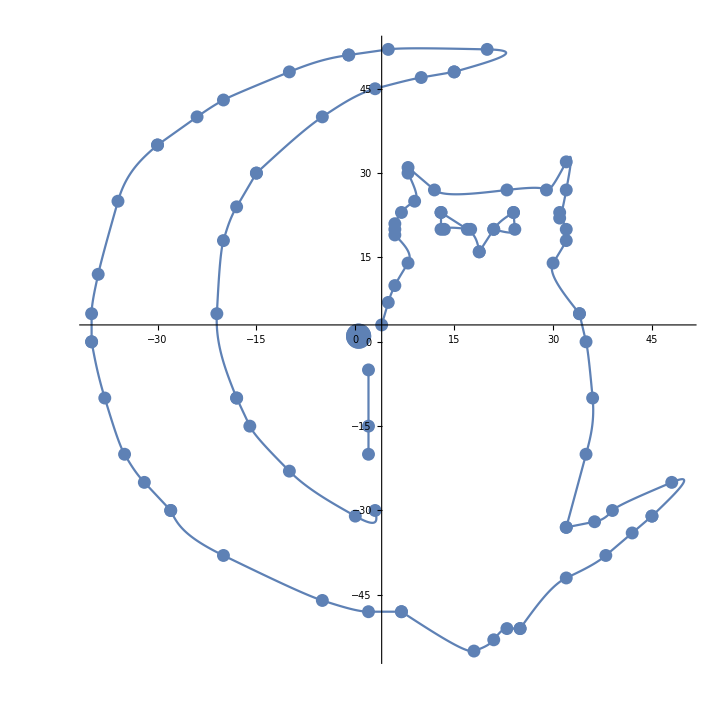

```mathematica
Show[cubic[({{4, 3}, {5, 7}, {6, 10}, {8, 14}, {6, 19}})(*linea cachete bajo izquierdo*)],cubic[({{6, 20}, {6, 21}, {7, 23}, {9, 25}, {8, 30}})(*linea cachete arriba izquierda*)],cubic[({{8, 31}, {12, 27}, {23, 27}, {29, 27}, {32, 32}, {32, 27}, {31, 22}})(*3.- oreja y cabeza*)],cubic[({{31, 23}, {32, 20}, {32, 18}, {30, 14}, {34, 5}})(*4.- cachete derecho*)],cubic[({{34, 5}, {35, 0}, {36, -10}, {35, -20}, {32, -33}})(*5.- cuerpo lado derecho *)],cubic[({{32, -33}, {36.3, -32}, {39, -30}, {48, -25}, {45, -31}})(*6.-union con luna*)],cubic[({{45, -31}, {42, -34}, {38, -38}, {32, -42}, {25, -51}})(*7.-*)],cubic[({{25, -51}, {23, -51}, {21, -53}, {18, -55}, {7, -48}})(*8.-prueba en el 8*)],cubic[({{7, -48}, {2, -48}, {-5, -46}, {-20, -38}, {-28, -30}})(*9.- cambiarle la union de luna*)],cubic[({{-28, -30}, {-32, -25}, {-35, -20}, {-38, -10}, {-40, 0}})(*10.-*)],cubic[({{-40, 0}, {-40, 5}, {-39, 12}, {-36, 25}, {-30, 35}})(*11*)],cubic[({{-30, 35}, {-24, 40}, {-20, 43}, {-10, 48}, {-1, 51}})(*12*)],cubic[({{-1, 51}, {5, 52}, {20, 52}, {15, 48}})(*13*)],cubic[({{15, 48}, {10, 47}, {3, 45}, {-5, 40}, {-15, 30}})(*14*)],cubic[({{-15, 30}, {-18, 24}, {-20, 18}, {-21, 5}, {-18, -10}})(*15*)],cubic[({{-18, -10}, {-16, -15}, {-10, -23}, {0, -31}, {3, -30}})(*16*)],cubic[({{2, -20}, {2, -15}, {2, -5}})],(*ojos*)
cubic[({{13, 23}, {17, 20}, {18.8, 16}})],cubic[({{18.8, 16}, {21, 20}, {24, 23}})],cubic[({{13, 23}, {13, 20}, {13.5, 20}, {17.5, 20}})],cubic[({{24, 23}, {24.2, 20}, {21, 20}})],ListPlot[{{.5,1}},PlotStyle->PointSize[.025]],ListPlot[({{4, 3}, {5, 7}, {6, 10}, {8, 14}, {6, 19}})(*1*)],ListPlot[({{6, 20}, {6, 21}, {7, 23}, {9, 25}, {8, 30}})(*2*)],ListPlot[({{8, 31}, {12, 27}, {23, 27}, {29, 27}, {32, 32}, {32, 27}, {31, 22}})(*3*)(*25,27*)(*31,27*)],ListPlot[({{31, 23}, {32, 20}, {32, 18}, {30, 14}, {34, 5}})(*4*)],ListPlot[({{34, 5}, {35, 0}, {36, -10}, {35, -20}, {32, -33}})(*5*)],ListPlot[({{32, -33}, {36.3, -32}, {39, -30}, {48, -25}, {45, -31}})(*6*)],ListPlot[({{45, -31}, {42, -34}, {38, -38}, {32, -42}, {25, -51}})(*7*)],ListPlot[({{25, -51}, {23, -51}, {21, -53}, {18, -55}, {7, -48}})(*8*)],ListPlot[({{7, -48}, {2, -48}, {-5, -46}, {-20, -38}, {-28, -30}})(*9*)],ListPlot[({{-28, -30}, {-32, -25}, {-35, -20}, {-38, -10}, {-40, 0}})(*10*)],ListPlot[({{-40, 0}, {-40, 5}, {-39, 12}, {-36, 25}, {-30, 35}})(*11*)],ListPlot[({{-30, 35}, {-24, 40}, {-20, 43}, {-10, 48}, {-1, 51}})(*12*)],ListPlot[({{-1, 51}, {5, 52}, {20, 52}, {15, 48}})(*13*)],ListPlot[({{15, 48}, {10, 47}, {3, 45}, {-5, 40}, {-15, 30}})(*14*)],ListPlot[({{-15, 30}, {-18, 24}, {-20, 18}, {-21, 5}, {-18, -10}})(*15*)],ListPlot[({{-18, -10}, {-16, -15}, {-10, -23}, {0, -31}, {3, -30}})(*16*)],ListPlot[({{2, -20}, {2, -15}, {2, -5}})],(*ojos*)ListPlot[({{13, 23}, {17, 20}, {18.8, 16}})],ListPlot[({{18.8, 16}, {21, 20}, {24, 23}})],ListPlot[({{13, 23}, {13, 20}, {13.5, 20}, {17.5, 20}})],ListPlot[({{24, 23}, {24.2, 20}, {21, 20}})],AspectRatio->1]
```

#### 6

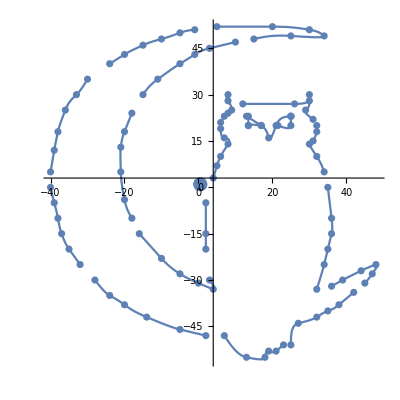

```mathematica
Show[cubic[({{4, 3}, {5, 7}, {6, 10}, {8, 14}, {7, 16}, {6, 19}})],cubic[({{6, 21}, {7, 23}, {8, 24}, {9, 25}, {8, 28}, {8, 30}})],cubic[({{12, 27}, {26, 27}, {30, 30}, {30, 28}, {29, 25}, {31, 22}})],cubic[({{32, 20}, {32, 18}, {31, 15}, {30, 14}, {32, 10}, {34, 5}})],cubic[({{35, 0}, {36, -10}, {36, -15}, {35, -20}, {34, -25}, {32, -33}})],cubic[({{36, -32}, {39, -30}, {44, -27}, {48, -25}, {47, -28}, {45, -31}})],cubic[({{42, -34}, {38, -38}, {35, -40}, {32, -42}, {27, -44}, {25, -51}})],cubic[({{23, -51}, {21, -53}, {19, -53}, {18, -55}, {13, -55}, {7, -48}})],cubic[({{2, -48}, {-5, -46}, {-14, -42}, {-20, -38}, {-24, -35}, {-28, -30}})],cubic[({{-32, -25}, {-35, -20}, {-37, -15}, {-38, -10}, {-39, -5}, {-40, 0}})],cubic[({{-40, 5}, {-39, 12}, {-38, 18}, {-36, 25}, {-33, 30}, {-30, 35}})],cubic[({{-24, 40}, {-20, 43}, {-15, 46}, {-10, 48}, {-5, 50}, {-1, 51}})],cubic[({{5, 52}, {20, 52}, {30, 51}, {34, 49}, {25, 49}, {15, 48}})],cubic[({{10, 47}, {3, 45}, {-1, 43}, {-5, 40}, {-11, 35}, {-15, 30}})],cubic[({{-18, 24}, {-20, 18}, {-21, 13}, {-21, 5}, {-20, -4}, {-18, -10}})],cubic[({{-16, -15}, {-10, -23}, {-5, -28}, {0, -31}, {4, -33}, {3, -30}})],cubic[({{2, -20}, {2, -15}, {2, -5}})],(*ojos*)
cubic[({{13, 23}, {17, 20}, {19, 16}, {21, 20}, {25, 23}})],cubic[({{13.5, 23}, {13.5, 20}, {13.5, 20}, {17, 20}})],cubic[({{25, 23}, {25, 23}, {25, 20}, {21.5, 20}})],ListPlot[{{.5,1}},PlotStyle->PointSize[.025]],ListPlot[({{4, 3}, {5, 7}, {6, 10}, {8, 14}, {7, 16}, {6, 19}})],ListPlot[({{6, 21}, {7, 23}, {8, 24}, {9, 25}, {8, 28}, {8, 30}})],ListPlot[({{12, 27}, {26, 27}, {30, 30}, {30, 28}, {29, 25}, {31, 22}})],ListPlot[({{32, 20}, {32, 18}, {31, 15}, {30, 14}, {32, 10}, {34, 5}})],ListPlot[({{35, 0}, {36, -10}, {36, -15}, {35, -20}, {34, -25}, {32, -33}})],ListPlot[({{36, -32}, {39, -30}, {44, -27}, {48, -25}, {47, -28}, {45, -31}})],ListPlot[({{42, -34}, {38, -38}, {35, -40}, {32, -42}, {27, -44}, {25, -51}})],ListPlot[({{23, -51}, {21, -53}, {19, -53}, {18, -55}, {13, -55}, {7, -48}})],ListPlot[({{2, -48}, {-5, -46}, {-14, -42}, {-20, -38}, {-24, -35}, {-28, -30}})],ListPlot[({{-32, -25}, {-35, -20}, {-37, -15}, {-38, -10}, {-39, -5}, {-40, 0}})],ListPlot[({{-40, 5}, {-39, 12}, {-38, 18}, {-36, 25}, {-33, 30}, {-30, 35}})],ListPlot[({{-24, 40}, {-20, 43}, {-15, 46}, {-10, 48}, {-5, 50}, {-1, 51}})],ListPlot[({{5, 52}, {20, 52}, {30, 51}, {34, 49}, {25, 49}, {15, 48}})],ListPlot[({{10, 47}, {3, 45}, {-1, 43}, {-5, 40}, {-11, 35}, {-15, 30}})],ListPlot[({{-18, 24}, {-20, 18}, {-21, 13}, {-21, 5}, {-20, -4}, {-18, -10}})],ListPlot[({{-16, -15}, {-10, -23}, {-5, -28}, {0, -31}, {4, -33}, {3, -30}})],ListPlot[({{2, -20}, {2, -15}, {2, -5}})],(*ojos*)ListPlot[({{13, 23}, {17, 20}, {19, 16}, {21, 20}, {25, 23}})],ListPlot[({{13.5, 23}, {13.5, 20}, {13.5, 20}, {17, 20}})],ListPlot[({{25, 23}, {25, 23}, {25, 20}, {21.5, 20}})],AspectRatio->1]
```